# PRÁCTICA 2 ECUACIONES EN DIFERENCIAS

## 1.- Introducción 2.- Ecuaciones en diferencias lineales homogéneas con coeficientes constantes 3.- Ecuaciones en diferencias lineales completas con coeficientes constantes 4.- Sistemas de ecuaciones en diferencias

1.-  INTRODUCCIÓN

En esta práctica vamos a estudiar ecuaciones de la forma:

                                      F ( t ,  y_t ,  y_(t + 1) ,   y_(t + 2) , ... ,  y_(t + n - 1) ,  y_(t + n)  ) = 0

siendo   t   una variable independiente que sólo toma los valores enteros  t = 0, 1, 2, ... . Las variables   { y_0 ,  y_1 ,  y_2 , ... }   representan el valor de la variable estudiada en un valor concreto de  t , es decir,   y_t = y (t)  es una variable dependiente.

Este tipo de expresiones se llamarán ecuaciones en diferencias (e.d.) y diremos que dicha ecuación tiene orden   k   si la diferencia entre el mayor y el menor subíndice de  y  es  k.

Las e.d. tienen especial interés en la resolución de problemas de las ciencias experimentales y sociales en los que se trata del estudio de la evolución temporal de determinadas variables (generalmente, la variable independiente   t   representa el número de periodos que han transcurrido desde un momento inicial  t = 0).

La diferencia fundamental entre las ecuaciones diferenciales y las ecuaciones en diferencias es que en las primeras se consideran variables continuas (toman valores en intervalos de números reales) mientras que en las segundas se consideran variables discretas (toman valores en números enteros o naturales)

EJEMPLO  1 :     y_(t+3)  -  y_(t+1)  -  5 y_t =  t^2          e.d. de orden  3     

                            y_(t+3)  +  3 y_(t+1)  = 5              e.d. de orden  2
        
                            y_(t+1)  +  4 y_t =  5  t^3             e.d. de orden  1   
        
                           5 y_(t+4) - 4 y_(t+2) + y_(t + 1) = ( (t - 2 ))^3     e.d. de orden  3

EJEMPLO  2 :  El número de infectados en una epidemia crece el triple en cada periodo de tiempo que transcurre entre dos medidas de lo que creció en el periodo anterior:

                                     y_(t+2)  -  y_(t+1)  =  3 . (y_(t+1) - y_t)  

simplificando tenemos    y_(t+2)  -   4 y_(t+1)  +  3 y_t = 0    que es una ecuación en diferencias de segundo orden.

EJEMPLO  3 :  El número de individuos de una población se duplica en cada generación y además se incorporan 10 individuos nuevos a esa población en cada generación:

                                   y_(t+2)  -  y_(t+1)  =  2 . (  y_(t+1)  -  y_t )  +  10     
       
simplificando tenemos     y_(t+2)  -  3 y_(t+1)  +  2 y_t  =  10    que es una ecuación en diferencias de segundo orden.

Este tipo de ecuaciones son muy comunes cuando se modelan situaciones que varían de un periodo a otro. Nuestro objetivo es encontrar la solución   y_t = y (t)   que describe el comportamiento de la función  y (t).

Llamamos  solución  general  de una e.d. al conjunto de todas las soluciones (tendrá tantos parámetros como orden tenga la ecuación). Para determinar esos parámetros necesitamos conocer unas condiciones iniciales, estas nos proporcionarán las distintas  soluciones  particulares.

Vamos a centrarnos en el caso de las ecuaciones en diferencias de la forma:

y_(t + n)  +   a_1 (t) . y_(t + n - 1)  + ...  +   a_(n - 1)  (t) . y_(t + 1)  +   a_n  (t) . y_t  =  b (t)

siendo   a_i(t)  y  b (t)    funciones de la variable   t, se llamarán ecuaciones en diferencias  lineales.

Las e.d. lineales se pueden clasificar en:

--   Homogéneas  si  b(t) = 0

--   Completas  si  b(t) ≠ 0

--   De  coeficientes  constantes    si   a_i(t)  =  a_i  ,  ∀ i

--   De  coeficientes  no  constantes  si  a_i(t)  ≠  a_i  ,  para algún  i

EJEMPLO  4 : 

(a)     8 y_(t+2)  -  5 y_t =  4       e.d. lineal, no homogénea, coeficientes constantes, orden 2

(b)      y_(t+1)  +  3 y_t  = 0        e.d. lineal,  homogénea, coeficientes constantes, orden 1

(c)   2 y_(t+1)  -  6 cos (2y_t) =  8     e.d. no lineal, no homogénea, coeficientes constantes, orden 1
   
(d)       y_(t+2)  +  y_t  =  2  + tg (t)    e.d. lineal,  no homogénea, coeficientes constantes, orden 2
    
(e)       y_(t+3)  +  5 y_(t+1)  =  y_t     e.d. lineal, homogénea, coeficientes constantes, orden 3
       
(f)       y_(t+3)  -  5 cos (y_t)  =  2      e.d. no lineal,  no homogénea, coeficientes constantes, orden 3
      
(g)       y_(t+2)  -  4 ⅇ t  +  y_t  =  24      e.d. lineal,  no homogénea, coeficientes constantes, orden 2
        
(h)       98  y_(t+5)  +  32 y_t  =  7      e.d. lineal, no homogénea, coeficientes constantes, orden 5
       
(i)       y_(t+1)  +  ⅇ^y_t  =  0      e.d. no lineal,  homogénea, coeficientes constantes, orden 1

(j)       y_(t+3) + 3 cos(t) y_(t+1) = 2      e.d. lineal, no homogénea, coeficientes no constantes, orden 2.

2.-  ECUACIONES  EN  DIFERENCIAS  LINEALES  HOMOGÉNEAS  CON  COEFICIENTES CONSTANTES

Vamos a considerar la ecuación diferencial    

               a_0 . y_(t + n)  +   a_1 . y_(t + n - 1)  + ...  +   a_(n - 1)  .  y_(t + 1)  +    a_n  .  y_t  =  0

siendo  a_i constantes,  se llamará   ecuación  en  diferencias  homogénea  con  coeficientes  constantes.



Si llamamos   y_t = 1 ,  y_(t + 1) =  λ ,   y_(t + 2) =  λ^2 , ... ,  y_(t + n) =  λ^n   se define la  ecuación  característica  asociada a dicha  e.d.  como:

               P (λ)  =  a_0  .  λ^n  +  a_1 .  λ^(n - 1) + ... +   a_(n - 1)  .  λ   +   a_n  = 0

Para resolver la e.d. debemos resolver la ecuación característica asociada, pueden ocurrir los siguientes casos:

1.-  todas sus raíces son reales y simples   r_1 ,  r_2 , ... ,   r_n ,  entonces
 
             y_H(t)  =  c_1 . r_1^t  +  c_2 . r_2^t  + ... +  c_n . r_n^t
             
2.-  todas sus raíces son reales pero   r_1   tiene multiplicidad   k   mientras que   r_2  , ... ,  r_n    son simples 
 
              y_H(t) = c_1 .  r_1^t   +  c_2 . t . r_1^t   + ... +  c_k . t^(k - 1) . r_1^t   +  c_(k + 1) . r_2^t   +  c_(k + 2) . r_3^t  +  ...  +  c_n . r_n^t   
             
3.-  tiene raíces complejas simples de la forma   a  -^+  b . ⅈ     entonces se calcula

          {r= √(a^2 + b^2)     (módulo)      
 α= arctg  (b/a)      (argumento)   →     y_H(t)  =   c_1 . r^t . cos ( α . t )  +   c_2 . r^t . sen ( α . t )  
      
4.-   tiene raíces complejas múltiples,   r  =  a  -^+  b . ⅈ    raíces complejas conjugadas de multiplicidad  m ,  entonces se calcula
 
         {r= √(a^2 + b^2)    (módulo)      
 α= arctg  (b/a)     (argumento)   →    y_H(t)  =  P_(m - 1)(t) . r^t . cos ( α . t )  +  Q_(m - 1) (t) .  r^t. sen ( α . t )  
      
siendo   P_(m - 1)(t)   y   Q_(m - 1)(t)   polinomios en   t   de grado menor o igual que   m - 1.

EJERCICIO  1:  Resolver las siguientes ecuaciones en diferencias homogéneas

( a )       y_(t + 3)  -  3 . y_(t + 2)  -  4 . y_(t + 1) +  12 . y_t =  0

```mathematica
Solve[λ^3-3 λ^2-4λ+12==0]
```

{{λ→-2},{λ→2},{λ→3}}

SOLUCIÓN :     y_(t)  =  c_1 . ( - 2 )^t +  c_2 . 2^t +  c_3 . 3^t

( b )       y_(t + 2)  -  4 . y_(t + 1) +  3 .  y_t =  0

```mathematica
Solve[λ^2 - 4λ + 3 == 0]
```

{{λ→1},{λ→3}}

( c )       y_(t + 2)  +  2 . y_(t + 1) +  y_t =  0

```mathematica
Solve[λ^2+2λ+1==0]
```

{{λ→-1},{λ→-1}}

SOLUCIÓN :    y_(t)  =  c_1 . (-1)^t +  c_2 . t . ( (- 1 ))^t

( d )       y_(t + 3)  -  4 . y_(t + 2)  +  5 . y_(t  + 1) - 2 . y_t =  0

```mathematica
Solve[λ^3 - 4 λ^2+5λ-2==0]+
```

{{λ→1},{λ→1},{λ→2}}

```mathematica
(*Solución: y(t)= c1 + c2.t + c3 * 2^t *)
```

( e )       y_(t + 3)  -  3 . y_(t + 2)  +  4 . y_(t + 1) - 12 . y_t =  0

```mathematica
Solve[λ^3-3 λ^2+4λ-12==0]
```

{{λ→-2 ⅈ},{λ→2 ⅈ},{λ→3}}

```mathematica
AbsArg[2ⅈ]
```

{2,π/2}

SOLUCIÓN :     y_(t)  =    c_1 . 3^t +  c_2 . 2^t. cos ( π/2. t )  +  c_3 . 2^t. sen ( π/2. t )

Mathematica

Usaremos la siguiente orden para resolver e.d.

      RSolve [ ecuación en diferencias , y [ t ] , t ]

EJERCICIO  2 :  Vamos a repetir el ejercicio anterior usando Mathematica

( a )       y_(t + 3)  -  3 . y_(t + 2)  -  4 . y_(t + 1) +  12 . y_t =  0

```mathematica
RSolve[y[t+3]-3y[t+2]-4y[t+1]+12y[t]==0,y[t],t]
```

{{y[t]→(-2)^t C[1]+2^t C[2]+3^t C[3]}}

SOLUCIÓN :     y_(t)  =  c_1 . ( - 2 )^t +  c_2 . 2^t +  c_3 . 3^t

( b )       y_(t + 2)  -  4 . y_(t + 1) +  3 .  y_t =  0

```mathematica
RSolve[y[t+2]-4y[t+1]+3y[t]==0,y[t],t]
```

{{y[t]→C[1]+3^t C[2]}}

( c )       y_(t + 2)  +  2 . y_(t + 1) +  y_t =  0

```mathematica
RSolve[y[t+2]-2y[t+1]+y[t]==0,y[t],t]
```

{{y[t]→C[1]+t C[2]}}

( d )       y_(t + 3)  -  4 . y_(t + 2)  +  5 . y_(t  + 1) - 2 . y_t =  0

```mathematica
RSolve[y[t+3]-4y[t+2]+ 5y[t+1] -2y[t]==0,y[t],t]
```

{{y[t]→C[1]+t C[2]+2^t C[3]}}

( e )       y_(t + 3)  -  3 . y_(t + 2)  +  4 . y_(t + 1) - 12 . y_t =  0

```mathematica
RSolve[y[t+3] - 3y[t+2] + 4y[t + 1] - 12y[t] == 0, y[t], t]
```

{{y[t]→(2 ⅈ)^t C[1]+(-2 ⅈ)^t C[2]+3^t C[3]}}

```mathematica
AbsArg[2ⅈ]
```

{2,π/2}

```mathematica
(*SOLUCIÓN:y_(t)=Subscript[c, 1] . 3^t+ Subscript[c, 2] .2^t.cos (π/2.t)+Subscript[c, 3] .2^t.sen (π/2.t) *)
```

Una vez calculada la solución general podremos imponer las condiciones necesarias para calcular todas las constantes que aparecen y obtener así una  solución particular .  En Mathematica debemos añadir las condiciones en forma de sistema de ecuaciones.

EJERCICIO  3 A :   Resolver la siguiente ecuacion en diferencias homogénea

                  y_(t + 3)  -  7 . y_(t + 2)  +  15 . y_(t  +  1)  -   9  .  y_t  =  0    
     
siendo    y (0) = - 1  ,    y (1) = 2  ,    y (2) = 17

Hacerlo primero resolviendo la ecuacion característica e imponiendo las condiciones.

La ecuacion característica es :        λ^3-7 λ^2+15λ-9=0

```mathematica
Solve[λ^3-7 λ^2+15λ-9==0]
```

{{λ→1},{λ→3},{λ→3}}

la solución general es:   y_ (t)  =  c_1 . 1^t +  c_2 . 3^t +  c_3 . t . 3^t    ⟶   y_(t)  =  c_1 +  c_2 . 3^t +  c_3 . t . 3^t  

vamos a definirla en Mathematica:

```mathematica
y[t_]=c1+c2*3^t+c3*t*3^t;
```

ahora imponemos las condiciones iniciales para calcular las constantes

          y (0) = - 1    ,     y (1) = 2    ,     y (2) = 17    

y resolvemos el sistema de ecuaciones

```mathematica
Solve[{y[0]==-1,y[1]==2,y[2]==17}]
```

{{c1→-1,c2→0,c3→1}}

por último asignamos estos valores a las constantes

```mathematica
c1=-1;
c2=0;
c3=1;
```

y así obtenemos la solución particular

```mathematica
y[t]
```

-1+3^t t

SOLUCIÓN :     y_(t)  =  - 1 +  t . 3^t

EJERCICIO  3 B :   Volver a resolver la misma ecuación en diferencias homogénea 

              y_(t + 3)  - 7 . y_(t + 2) + 15 . y_(t  +  1) -  9  .  y_t  =  0           siendo    y (0) = - 1  ,  y (1) = 2  ,  y (2) = 17 

usando ahora la orden  RSolve.

```mathematica
Clear["Global` *"]
```

```mathematica
RSolve[f[t+3] - 7 f[t+2] + 15f[t+1] - 9f[t]== 0, f[t], t]
```

{{f[t]→C[1]+3^t C[2]+3^t t C[3]}}

```mathematica
g[t_]=c1+c2*3^t+c3*t*3^t
```

c1+3^t c2+3^t c3 t

```mathematica
Solve[{g[0]==-1,g[1]==2,g[2]==17}]
```

{{c1→-1,c2→0,c3→1}}

Mathematica

Suele ser interesante representar gráficamente la solución particular, usaremos la siguiente orden de Mathematica :

      DiscretePlot  [  y [ t ]  / .  sol [ [ 1 ] ]  ,  { t , 0 , valor superior de t } ]

EJERCICIO  3 C :   Representar gráficamente los 11 primeros valores de la solución de la e.d. anterior.

```mathematica
Table[g[t]/.sol[[1]],{t,0,10}]
```

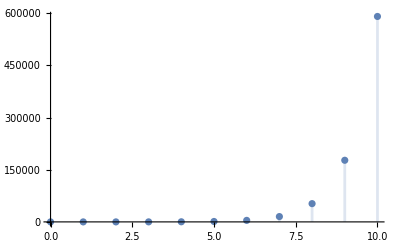

```mathematica
DiscretePlot[y[t]/.sol[[1]],{t,0,10},PlotRange->All]
```

Mathematica

A veces podemos necesitar una tabla de valores de la solución, usaremos la siguiente orden de Mathematica :

      Table  [  y [ t ]  / .  sol [ [ 1 ] ]  ,  { t , 0 , valor superior de t } ]

EJERCICIO  3 D :   Dar una tabla de los   11   primeros valores de la solución de la e.d. anterior.

```mathematica
Table[y[t]/.sol[[1]],{t,0,10}]
```

{-1,2,17,80,323,1214,4373,15308,52487,177146,590489}

EJERCICIO  4 :  Dada la siguiente ecuación en diferencias homogénea

     y_(t + 2)  -  5 . y_(t + 1)  -  6 . y_t  =  0    siendo    y (0) = 1  ,  y (1) = 3

( 4.A )  Resolver a partir de la ecuacion característica e imponiendo las condiciones.

```mathematica
Solve[λ^2-5λ - 6==0]
```

{{λ→-1},{λ→6}}

La solución general es de la forma : y(t) = c1.(-1)^t + c2. 6^t

```mathematica
y[t_] = c1 * (-1)^t + c2 * 6^t
```

(3 (-1)^t)/7+1/7 2^(2+t) 3^t

```mathematica
Solve[{y[0] == 1, y[1] == 3}]
```

{{c1→3/7,c2→4/7}}

```mathematica
c1 = 3/7;
c2 =4/7;
y[t]
```

(3 (-1)^t)/7+1/7 2^(2+t) 3^t

Luego, la solución particular de la ecuación en diferencias homogénea es: y(t) =(3 (-1)^t)/7+1/7 2^(2+t) 3^t

( 4.B )   Resolver  usando la orden  RSolve 

             y_(t + 2)  -  5 . y_(t + 1)  -  6 . y_t  =  0    siendo    y (0) = 1  ,  y (1) = 3

```mathematica
Clear["Global`*"]
```

```mathematica
RSolve[{h[t +2] -5 h[t+1] - 6h[t] == 0, h[0] ==1,h[1] == 3},h[t], t]
```

{{h[t]→1/7 (3 (-1)^t+2^(2+t) 3^t)}}

```mathematica
j[t_] = (-1)^t* c1+6^t *c2
```

(-1)^t c1+6^t c2

Luego, la solución particular de la ecuación en diferencias homogénea es: y(t) =1/7 (3 (-1)^t+2^(2+t) 3^t)

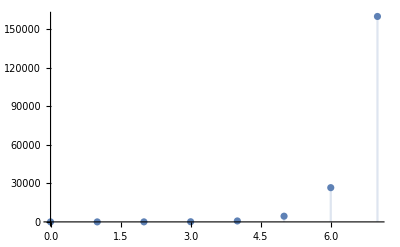

```mathematica
(*4c*)
y[t_]=(3 (-1)^t)/7+1/7 2^(2+t) 3^t;
DiscretePlot[y[t], {t, 0, 7}, PlotRange->All]
```

( 4.D )  Dar una tabla de los   15   primeros valores de la solución de la e.d. anterior.

```mathematica
Table[y[t], {t, 0, 14}]
```

{1,3,21,123,741,4443,26661,159963,959781,5758683,34552101,207312603,1243875621,7463253723,44779522341}

EJERCICIO  5 :  Dada la siguiente ecuación en diferencias homogénea

     y_(t + 2)  -  y_(t + 1)  +  y_t  =  0    siendo    y (0) = 0  ,  y (1) = 1

( 5.A )  Resolver a partir de la ecuación característica e imponiendo las condiciones.

```mathematica
Clear["Global`*"]
```

```mathematica
Solve[λ^2-λ + 1==0]
```

{{λ→(-1)^(1/3)},{λ→-(-1)^(2/3)}}

```mathematica
y[t_] = c1 * (-1^(1/3))^t + c2 *(-(-1)^(2/3))^t
```

(-1)^t c1+(-(-1)^(2/3))^t c2

```mathematica
Solve[{y[0] == 0, y[1] == 1}]
```

{{c1→1/(-1+(-1)^(2/3)),c2→-1/(-1+(-1)^(2/3))}}

```mathematica
c1 = 1/(-1+(-1)^(2/3))
```

1/(-1+(-1)^(2/3))

```mathematica
c2 = -1/(-1+(-1)^(2/3))
```

-1/(-1+(-1)^(2/3))

```mathematica
y[t]
```

(-1)^t/(-1+(-1)^(2/3))-((-(-1)^(2/3))^t)/(-1+(-1)^(2/3))

La solución general es de la forma : y(t) = (-1)^t/(-1+(-1)^(2/3))-((-(-1)^(2/3))^t)/(-1+(-1)^(2/3))

( 5.B )   Resolver  usando la orden  RSolve 

              y_(t + 2)  -  y_(t + 1)  +  y_t  =  0    siendo    y (0) = 0  ,  y (1) = 1

```mathematica
Clear["Global`*"]
```

```mathematica
RSolve[{y[t+2] - y[t+1] + y[t] == 0, y[0] == 0, y[1] == 1}, y[t], t]
```

{{y[t]→(ⅈ ((1/2-(ⅈ √3)/2)^t-(1/2+(ⅈ √3)/2)^t))/(√3)}}

( 5.C )   Representar gráficamente  los  14  primeros valores de la solución.

```mathematica
y[t_] = (ⅈ ((1/2-(ⅈ √3)/2)^t-(1/2+(ⅈ √3)/2)^t))/(√3)
```

(ⅈ ((1/2-(ⅈ √3)/2)^t-(1/2+(ⅈ √3)/2)^t))/(√3)

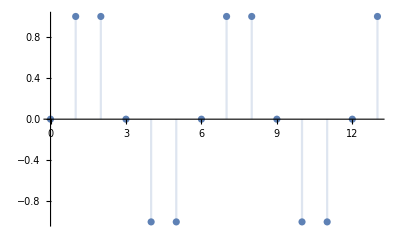

```mathematica
DiscretePlot[y[t], {t, 0, 13}]
```

(5.D )  Dar una tabla de los   4   primeros valores de la solución de la e.d. anterior.

```mathematica
Table[y[t], {t, 0, 3}]
```

{0,1,(ⅈ ((1/2-(ⅈ √3)/2)^2-(1/2+(ⅈ √3)/2)^2))/(√3),(ⅈ ((1/2-(ⅈ √3)/2)^3-(1/2+(ⅈ √3)/2)^3))/(√3)}

Mathematica

También podemos usar la siguiente orden para resolver e.d.

        sol = RSolveValue [ ecuación en diferencias , y [ t ] , t ]
      
      
en este caso para representar gráficamente la solución particular usaremos la orden

        DiscretePlot  [ sol ,  { t , 0 , valor superior de t } ]
      
(esta gráfica nos puede indicar la convergencia de la solución)


y para obtener una tabla de valores de la solución usaremos :

        Table  [  sol  ,  { t , 0 , valor superior de t } ]

EJERCICIO  6 :  Dada la siguiente ecuación en diferencias homogénea

      y_(t + 1) =  0,8 . y_t        siendo    y (0) = 500

( 6.A )  Resolver a partir de la ecuacion característica e imponiendo las condiciones.

```mathematica
Clear["Global`*"]
```

La ecuación característica es   λ-0.8=0   y vamos a resolverla

```mathematica
Solve[λ-0.8==0]
```

{{λ→0.8}}

la solución general es:
           
                   y_H(t)  =  c_ . 0.8^t 
                   
vamos a definirla en Mathematica:

```mathematica
y[t_]=c*0.8^t;
```

ahora vamos a imponer la condición inicial :    y (0) = 500  para calcular la constante resolviendo la ecuación que resulta

```mathematica
Solve[{y[0]==500}]
```

por último asignamos ese valor a la constante

```mathematica
c=500;
```

y así obtenemos la solución particular

```mathematica
y[t]
```

SOLUCIÓN :     y_(t)  =  500 . 0.8^t

( 6.B )   Resolver  usando la orden   RSolve  y la orden   RSolveValue

                y_(t + 1) =  0,8 . y_t        siendo    y (0) = 500

```mathematica
Clear["Global`*"]
```

```mathematica
sol=RSolve[{y[t+1]-0.8*y[t]==0,y[0]==500},y[t],t]
```

{{y[t]→500. 1.25^(-1. t)}}

```mathematica
sol=RSolveValue[{y[t+1]-0.8*y[t]==0,y[0]==500},y[t],t]
```

500. 1.25^(-1. t)

SOLUCIÓN :     y_(t)  =  500 . 0.8^t

( 6.C )   Representar  gráficamente los  80  primeros valores de la solución.

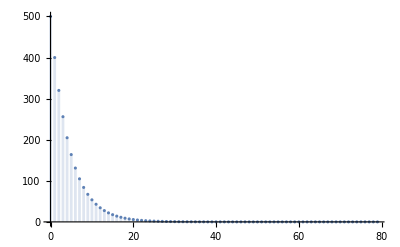

```mathematica
DiscretePlot[sol,{t,0,79},PlotRange->All]
```

( 6.D )  Dar una tabla de los   21   primeros valores de la solución de la e.d. anterior.

```mathematica
Table[sol,{t,0,20}]
```

{500.,400.,320.,256.,204.8,163.84,131.072,104.858,83.8861,67.1089,53.6871,42.9497,34.3597,27.4878,21.9902,17.5922,14.0737,11.259,9.0072,7.20576,5.76461}

3.-  ECUACIONES  EN  DIFERENCIAS  LINEALES  COMPLETAS  CON  COEFICIENTES CONSTANTES

Consideramos la ecuación diferencial 

                     y_(t+n)  +   a_1 y_(t+n-1)  + ...  +   a_(n-1)  y_(t+1) +   a_n  y_t  =   b (t)

siendo  a_i constantes  y  b (t) ≠ 0,  se llamará ecuacion en diferencias completa con coeficientes constantes.

La solución general de la e.d. completa se obtiene sumando la solución general de la ecuación homogénea con la particular de la completa, es decir

                       y (t)  =  y_H(t)  +   y_P(t) 
             
             
Para calcular la solución particular de la e.d. completa podemos usar alguno de los siguientes métodos:

Método  de variación  de  los  parámetros

Este método parte de la  solución general de la e.d. homogénea y  supone que las constantes dependen de  t ,  es decir,  c_i =  c_i (t).

Método de los coeficientes indeterminados

Este método busca una solución particular dependiendo de la forma del término independiente  b (t), la siguiente tabla muestra los casos mas comunes : 

 b (t) | no raiz | raiz de multiplicidad  m  | y_P(t)
c | 1 | - | k
c | - | 1 | k t^m
P_n(t) | 1 | - | Q_n(t)
P_n(t) | - | 1 | t^m Q_n(t)
r^t | r | - | k r^t
r^t | - | r | k t^m r^t
r^t P_n(t) | r | - | r^t Q_n(t)
r^t P_n(t) | - | r | r^t t^m Q_n(t)
a cos (αt) + b sen (αt) |  cos (α) + ⅈ sen (α) | - | A cos (αt) +  B  sen (αt)
a cos (αt) + b sen (αt) | - |  cos (α) + ⅈ sen (α) | t^m( A cos (αt) +  B  sen (αt))
r^t( a cos (αt) + b sen (αt)) | r ( cos (α) + ⅈ sen (α) ) | - | r^t( A cos (αt) +  B  sen (αt))
r^t( a cos (αt) + b sen (αt)) | - | r ( cos (α) + ⅈ sen (α) ) | r^t t^m( A cos (αt) +  B  sen (αt))

podemos resumir la tabla anterior en:

◼  si  b(t) = r^t  entonces para encontrar la solución de la ecuación completa  probamos con 
       
       ◼ ◼   la solución particular   k r^t   si   r   no es solución de la ecuación característica
       ◼ ◼   la solución particular   k t r^t   si   r  es solución de la ecuación característica con multiplicidad  1
       ◼ ◼   la solución particular  k t^2 r^t  si  r es solución de la ecuación característica con multiplicidad 2


◼  si  b(t)  es un polinomio de grado n   entonces para encontrar la solución de la ecuación completa  probamos con 
     
       ◼ ◼  un polinomio de grado   n    si  el  1  no es raíz de la ecuación característica 
       ◼ ◼  un polinomio de grado   n + 1    si  el  1  es raíz de la ecuación característica con multiplicidad  1
       ◼ ◼  un polinomio de grado   n + 2    si  el  1  es raíz de la ecuación característica con multiplicidad  2


◼  si  b(t)  es  seno  o  coseno  de  ( α t )   entonces para encontrar la solución de la ecuación completa  probamos con   A . cos (αt )  +  B.  sen (αt)

EJERCICIO  1 :  Resolver la siguiente ecuación en diferencias completa

                                     y_(t + 2)  -   5 . y_(t + 1)  +   6 . y_t  =  10

```mathematica
Clear["Global`*"]
```

```mathematica
RSolve[y[t+2]-5y[t+1]+6y[t]==10,y[t],t]
```

{{y[t]→5+2^t C[1]+3^t C[2]}}

SOLUCIÓN :     y_(t)  =  5  +  c_1 .  2^t  +  c_2 .  3^t

EJERCICIO  2 :  Resolver la siguiente ecuación en diferencias completa

                                     y_(t + 2)  -   3 . y_(t + 1)  +   2 . y_t  -  4  =  0

```mathematica
Clear["Global`*"]
```

```mathematica
RSolve[y[t+2] - 3y[t+1] + 2y[t] == 4, y[t], t]
```

{{y[t]→-4 (1+t)+C[1]+2^t C[2]}}

EJERCICIO  3 :  Resolver la siguiente ecuación en diferencias completa

                                     y_(t + 2)  -   3 . y_(t + 1)  +   2 .  y_t  =  3^t

```mathematica
Clear["Global`*"]
```

```mathematica
RSolveValue[y[t+2] - 3y[t+1] + 2y[t] == 3^t, y[t], t]
```

3^t/2+C[1]+2^t C[2]

EJERCICIO  4 :  Resolver la siguiente ecuación en diferencias completa

                                     y_(t + 2)  -   3 .  y_(t + 1)  +   2 .  y_t  =  2^t

```mathematica
Clear["Global`*"]
```

```mathematica
RSolveValue[y[t+2] - 3y[t+1] + 2y[t] == 2^t, y[t], t]
```

2^(-1+t) (-2+t)+C[1]+2^t C[2]

EJERCICIO  5 :   Dada la siguiente ecuación en diferencias completa

      2 . y_(t + 2)  =   11 .  y_(t + 1)  -   12 . y_t +  0,5 . t     siendo  y (0) = 5  ,  y (1) = 12

( 5.A )  Resolverla

( 5.B )  Representar  los  20  primeros valores de la solución.

( 5.C )  Calcular los  10  primeros valores de la serie.

EJERCICIO  6 :   Dada la siguiente ecuación en diferencias completa

                                 x_(t + 2)  - x_(t + 1)  =  1/4 . ( x_(t + 1)  -  x_t )  +  2 . t

( 6.A )   Resolver la correspondiente  e.d.  homogénea asociada

( 6.A.1)   Resolviendo la ecuacion característica e imponiendo las condiciones.

```mathematica
Clear["Global`*"]
```

La  e.d.  dada es: 
 
 x_(t + 2)  -  x_(t + 1) -  1/4 . ( x_(t + 1)  -  x_t )  =  2 . t      ⟶   x_(t + 2)  -  x_(t + 1) -  1/4 .  x_(t + 1)  +  1/4 .  x_t   =  2 . t    ⟶    x_(t + 2)   -  5/4 .  x_(t + 1)  +  1/4 .  x_t   =  2 . t 

por tanto, su e.d.  homogénea asociada es:
  
         x_(t + 2)   -  5/4 .  x_(t + 1)  +  1/4 .  x_t   =  0

y la ecuacion característica es :        λ^2-5/4 λ +1/4= 0    , vamos a resolverla

```mathematica
Solve[λ^2-5/4 λ+1/4==0]
```

luego la solución de la homogénea es: 

              y_H(t)  =  c_1 . (1/4)^t +  c_2 . 1^t    ⟶   y_H(t)  =  c_1 . (1/4)^t +  c_2

SOLUCIÓN :     y_H(t)  =   c_1 . (1/4)^t  +   c_2

( 6.A.2)   Usando la correspondiente orden de Mathematica

( 6.B)   Resolver la correspondiente  e.d.  completa 
  
                                   x_(t + 2)  - x_(t + 1)  =  1/4 . ( x_(t + 1)  -  x_t )  +  2 . t

( 6.C)   Resolver la correspondiente  e.d.  completa con las condiciones iniciales:
  
                x_(t + 2)  - x_(t + 1)  =  1/4 . ( x_(t + 1)  -  x_t )  +  2 . t     con    x ( 0 ) = 100   y   x ( 1 ) = 180

( 6.D )   Calcular   x (4) .

( 6.E )   Representar  los  30  primeros valores de la serie.

( 6.F )   Calcular   los  5  primeros valores.

EJERCICIO  7 :    Dada la siguiente ecuación en diferencias completa

                 x_(t + 2)  +  x_(t + 1)  =  - 3 . x_t  -  2^t

( 7.A )   Resolver la correspondiente  e.d.  homogénea asociada

( 7.A.1)   Resolviendo la ecuacion característica e imponiendo las condiciones.

( 7.A.2)   Usando la correspondiente orden de Mathematica

( 7.B)   Resolver la correspondiente  e.d.  completa 
  
                                      x_(t + 2)  +  x_(t + 1)  =  - 3 . x_t  -  2^t

( 7.C)   Resolver la correspondiente  e.d.  completa con las condiciones iniciales:
  
                x_(t + 2)  +  x_(t + 1)  =  - 3 . x_t  -  2^t        con    x ( 0 ) = 1   y   x ( 1 ) = 2

(7.D )   Representar  los   21   primeros valores de la solución.

(7.E )    Calcular los   8   primeros valores de la serie.

EJERCICIO  8 :   Supongamos que, si no intervienen factores externos, el incremento del número de individuos en un mes es las tres cuartas partes del incremento del mes anterior. Además cada mes se incorporan 25 individuos a la población.
Inicialmente en la población hay  10  individuos  y al finalizar el primer mes hay 30  individuos.
La ecuación general que modeliza la evolución de dicha población es 

        y_(t + 2) -  y_(t + 1)  = 3/4 . ( y_(t + 1) - y_t )  +  25     siendo  y (0) = 10  ,  y (1) = 30.

( 8.A )   Resolver esa ecuación en diferencias.

( 8.B )   Calcular el número de individuos que tiene la población en el cuarto mes.

( 8.C )   Representar gráficamente la evolución del número de individuos de la población (hasta t = 18).

( 8.D )   Calcular los  5  primeros valores de la serie y comprobar que coinciden los dos valores iniciales dados y el resultado del cuarto mes.

4.-  SISTEMAS DE ECUACIONES  EN  DIFERENCIAS  LINEALES

Cuando al estudiar un fenómeno discreto aparece más de una variable plantearemos un sistema de ecuaciones en diferencias. Solo estudiaremos sistemas de e.d. lineales y de primer orden con coeficientes constantes.

Veremos primero el caso particular de un sistema de e.d. lineal homogéneo de la forma :

          {x_(t+1)= a x_t  +  b  y_t 
  y_(t+1)= c x_t + d  y_t      
 
que se puede expresar de forma matricial para facilitar su resolución

                ( x_(t+1)
y_(t+1))  =  ( a | b
c | d )  ( x_t
y_t)

EJERCICIO  1 :  Resolver el siguiente sistema de ecuaciones en diferencias

                                                  {x_(t + 1)= 4 . x_t -  y_t   
 y_(t + 1)= 2 . x_t + y_t

```mathematica
Clear["Global`*"]
```

```mathematica
eqns={x[t+1]==4x[t]-y[t],y[t+1]==2x[t]+y[t]};
```

```mathematica
sol=RSolve[eqns,{x,y},t]
```

SOLUCIÓN :     x_(t)  = ( - 2^t + 2 .  3^t )  .  c_1 + ( 2^t- 3^t )  .  c_2 
                           y_(t)  =  - 2 . ( 2^t - 3^t )  .  c_1 + ( 2^(1 + t)- 3^t )  .  c_2

EJERCICIO  2 :   Dado el siguiente sistema de ecuaciones en diferencias

                  {x_(t + 1)=  x_t + 3 . y_t   
 y_(t + 1)= 4 . x_t                        siendo    { x_0= 1     
 y_0= - 4

( 2.A )   Resolver.

( 2.B )    Comprobar los valores iniciales y calcular los valores en   t = 8.

( 2.C )   Representar los primeros  7  valores de  la solución  ( x (t) , y (t) ).

Al igual que ocurre cuando se tiene una sola e.d.,  la solución general del sistema de ecuaciones en diferencias no homogéneo se obtiene sumando una solución particular del sistema y la solución general del sistema homogéneo asociado.

Dado un sistema de e.d. lineal no homogéneo de la forma :

           { x_(t + 1)= a  . x_t  +  b . y_t  + g (t)
  y_(t+1)= c . x_t + d . y_t  + h (t)       
 
se puede expresar de forma matricial para facilitar su resolución

                ( x_(t + 1)
y_(t + 1))  =  ( a   | b
c   | d )  ( x_t
y_t)  + ( g (t)
 h (t))

EJERCICIO  3 :   Resolver el siguiente sistema de ecuaciones en diferencias

      {x_(t + 1)= 2 . t  +  7 . x_t  -  4 . y_t 
y_(t + 1)=  6 . x_t -   3 . y_t                          siendo    {x_0= 14          
y_0=  21

```mathematica
Clear["Global`*"]
```

```mathematica
eqns={x[t+1]==2t+7x[t]-4y[t],y[t+1]==6 x[t]-3y[t],x[0]==14,y[0]==21};
```

```mathematica
sol=RSolve[eqns,{x,y},t]
```

SOLUCIÓN :     x_(t)  =  1/2 . ( 25 + 3^(1 + t) - 2 . t -4 . t^2 )
                              y_(t)  =  3/2 . (13 + 3^t-2 . t^2 )

EJERCICIO  4 :    Dado el siguiente sistema de ecuaciones en diferencias

       {x_(t + 1)=  2 . x_t - 3 . y_t - 1
y_(t + 1)= x_t -  2 . y_t + t              siendo    {x_5= 30 
 y_5=  80

( 4.A )    Resolver.

( 4.B )    Comprobar los valores iniciales y calcular los valores en   t = 10.

( 4.C )   Representar los primeros  10  valores de  la solución  ( x (t) , y (t) ).

EJERCICIO  5 :    Dado el siguiente sistema de ecuaciones en diferencias

       {x_(t + 1)= 3 . x_t - y_t + 1      
y_(t + 1)= - x_t + 2 . y_t + 3          siendo    {x_0= 150 
 y_0=  325

( 5.A )    Resolver.

```mathematica
Clear["Global`*"]
```

```mathematica
eqns={x[t+1]==3x[t]-y[t]+1,y[t+1]==-x[t]+2y[t]+3,x[0]==150,y[0]==325};
```

```mathematica
sol=RSolve[eqns,{x,y},t]//N
```

SOLUCIÓN :   
    
      x_(t)  = 0.2 2.^(-1. t) (-5. 2.^(2.+t)+385. 2.76393^t+255. 2.23607 2.76393^t+385. 7.23607^t-255. 2.23607 7.23607^t)
      y_(t)  = 0.2 2.^(-1. t) (-35. 2.^t+830. 2.76393^t+320. 2.23607 2.76393^t+830. 7.23607^t-320. 2.23607 7.23607^t)

( 5.B )    Comprobar los valores iniciales y calcular los valores en   t = 3.

vamos a definir las funciones solución para poder evaluarlas

```mathematica
x[t_]=0.2 2.^(-1. t) (-5. 2.^(2.+t)+385. 2.76393202250021^t+255. 2.23606797749979 2.76393202250021^t+385. 7.23606797749979^t-255. 2.23606797749979 7.23606797749979^t);
y[t_]=0.2 2.^(-1. t) (-35. 2.^t+830. 2.76393202250021^t+320. 2.23606797749979 2.76393202250021^t+830. 7.23606797749979^t-320. 2.23606797749979 7.23606797749979^t);
```

```mathematica
x[0]
y[0]
```

```mathematica
x[3]
y[3]
```

SOLUCIÓN :     x_(3)  =  - 1254
                               y_(3)  =  1893

( 5.C )   Representar los primeros  15  valores de  la solución  ( x (t) , y (t) ).

```mathematica
DiscretePlot[{x[t],y[t]},{t,0,14},PlotRange->All]
```

EJERCICIO  6 :   Dado el siguiente sistema de ecuaciones en diferencias

        {x_(t+1)= 2 x_t -  3  y_t 
 y_(t+1)=x_t - 2 y_t                  siendo    { x_0= 100
y_0=  50

( 6.A )    Resolver.

( 6.B )    Comprobar los valores iniciales y calcular los valores en  t = 10  y en   t = 11.

EJERCICIO   6 C :   Representar los primeros  12  valores de  la solución  (x(t) , y(t) ).